```mathematica
ClearAll[]

fact = 178.9818;
time=0.1;
dim=12;

Γ=Import["C:\\Users\\aless\\OneDrive - Università degli Studi di Parma\\Documents\\Lavoro\\QEC_FT\\optimization_codewords\\Gamma_08apr.txt","Table"]*fact;
γ=Array[0,{dim,dim}];
Do[γ[[m,n]]=2*Γ[[m,n]]-Γ[[m,m]]-Γ[[n,n]],{m,dim},{n,dim}];
χ=Exp[γ*time];
{eigs,vecs}=Eigensystem[χ];
(* vecs[[1]]=-vecs[[1]];
vecs[[4]]=-vecs[[4]];*)

Pr=ConstantArray[0,{dim,dim}];
Do[Pr[[k,k]]=1,{k,dim}];

(* Error operators *)
Er =ConstantArray[0,{dim,dim}];
Do[Do[Er[[j,k]]=Er[[j,k]]+Sqrt[eigs[[k]]]*vecs[[k,m]]*Pr[[j,m]],{j,dim},{m,dim}],{k,dim}]
```

```mathematica
(*Er[[All,2]]=-Er[[All,2]];*)
MatrixForm[Er]
```

(-0.921553 | 0.381186 | 0.0735496 | -0.00529023 | -0.000298656 | 0.0000418767 | 0.+0.0000161259 ⅈ | 3.70413×10^-6 | -2.18329×10^-8 | 0.-1.89883×10^-6 ⅈ | 0.-8.27663×10^-7 ⅈ | 2.5354×10^-7
-0.921613 | -0.381059 | 0.0734544 | 0.00527403 | -0.000295279 | -0.0000417723 | 0.+0.000013837 ⅈ | 4.6638×10^-6 | -1.61723×10^-6 | 0.+2.84583×10^-6 ⅈ | 0.+7.9052×10^-7 ⅈ | 5.16316×10^-7
-0.997261 | 0.0631045 | -0.0384188 | 0.00344109 | -0.000307062 | 0.0000143282 | 0.-3.07053×10^-6 ⅈ | -0.0000169627 | 1.08686×10^-6 | 0.+3.87882×10^-6 ⅈ | 0.+7.58196×10^-6 ⅈ | 1.36027×10^-6
-0.997286 | -0.0626919 | -0.0384579 | -0.00342489 | -0.000309171 | -0.0000182767 | 0.-0.0000120316 ⅈ | -2.94272×10^-6 | -1.50265×10^-6 | 0.-6.5201×10^-6 ⅈ | 0.-4.35028×10^-6 ⅈ | -8.31054×10^-6
-0.930843 | 0.360401 | 0.0603283 | -0.00187444 | 0.000290229 | -0.0000506415 | 0.-0.0000214542 ⅈ | -4.90204×10^-6 | -1.02109×10^-7 | 0.+2.6419×10^-6 ⅈ | 0.+1.12783×10^-6 ⅈ | -2.99651×10^-7
-0.930782 | -0.360545 | 0.0604062 | 0.00190119 | 0.000285228 | 0.0000503209 | 0.-0.0000183084 ⅈ | -6.0518×10^-6 | 2.25221×10^-6 | 0.-3.86862×10^-6 ⅈ | 0.-1.12246×10^-6 ⅈ | -6.33597×10^-7
-0.993435 | 0.109529 | -0.0325342 | 0.0056089 | -0.0000443063 | 0.0000174082 | 0.-0.0000222592 ⅈ | 0.0000197797 | 9.37468×10^-8 | 0.+2.04348×10^-6 ⅈ | 0.+3.82647×10^-6 ⅈ | -8.28551×10^-7
-0.993423 | -0.109645 | -0.0325174 | -0.00561798 | -0.0000422015 | -9.96013×10^-6 | 0.-1.18175×10^-6 ⅈ | 2.28746×10^-6 | 0.0000170473 | 0.+3.1561×10^-6 ⅈ | 0.-3.65049×10^-6 ⅈ | 4.35193×10^-6
-0.992027 | 0.122158 | -0.0303742 | 0.00610548 | 0.0000477738 | 9.48626×10^-6 | 0.+3.15386×10^-6 ⅈ | -3.54264×10^-6 | -8.09228×10^-6 | 0.+5.9504×10^-6 ⅈ | 0.-0.0000100617 ⅈ | 2.87116×10^-6
-0.991996 | -0.12242 | -0.0303291 | -0.00611929 | 0.0000494438 | -0.0000119907 | 0.-1.56997×10^-6 ⅈ | 2.2137×10^-6 | -0.0000104187 | 0.-8.73175×10^-6 ⅈ | 0.+2.3865×10^-6 ⅈ | 7.12954×10^-6
-0.98751 | 0.155631 | -0.0234682 | 0.00716241 | 0.000311803 | -0.0000105468 | 0.+0.0000279665 ⅈ | -3.3116×10^-7 | 5.9382×10^-6 | 0.-8.95512×10^-6 ⅈ | 0.+1.36683×10^-6 ⅈ | -1.7187×10^-6
-0.987507 | -0.155654 | -0.023466 | -0.00716627 | 0.000311754 | 9.76764×10^-6 | 0.+0.0000187928 ⅈ | 2.0843×10^-6 | -4.66358×10^-6 | 0.+9.45789×10^-6 ⅈ | 0.+2.93244×10^-6 ⅈ | -4.6917×10^-6)

```mathematica
acc=0;
Do[acc=acc+Er[[k,j]]*Er[[k,j]],{k,dim},{j,dim/2}]
1-acc/dim
```

-1.78243×10^-10

```mathematica
b=ConstantArray[0,{dim}];
Do[b[[k]]=1,{k,dim-1,dim}];
B=ConstantArray[0,{dim,dim}];
A=ConstantArray[0,{38,dim}];
z=ConstantArray[0,dim];
zL=ConstantArray[0,{dim}];
oL=ConstantArray[0,{dim}];
ew0=ConstantArray[0,{dim/2,dim}];
ew1=ConstantArray[0,{dim/2,dim}];
inds={1,2,3,4,5,7,8,9,12,13};
```

```mathematica
(* code words*)
x =1;
While[x>1/1000000,
zero=Sort[Join[RandomSample[{1,3,5,7,9,11},3],RandomSample[{2,4,6,8,10,12},3]]];
(*zero ={2,4,5,7,9,12};*)
uno=Complement[Range[dim],zero];
cw=Flatten[{zero, uno}];
Do[z[[k]]=1,{k,dim/2+1,dim}];

Do[m=1; Do[Do[A[[m,j]]=Sqrt[eigs[[k]]*eigs[[l]]]*vecs[[l,cw[[j]]]]*vecs[[k,cw[[j]]]]*(-1)^z[[j]];m=m+1,{l,k,dim/2}],{k,1,dim/2}],{j,1,dim}];

Do[B[[j,k]]=A[[inds[[j]],k]],{j,1,dim-2},{k,1,dim}];
Do[B[[dim-1,k]]=z[[k]],{k,1,dim}];
Do[B[[dim,k]]=1-z[[k]],{k,1,dim}];
x=Total[Abs[Im[Sqrt[PseudoInverse[B, Tolerance->10^(-15)].b]]]]]
y=Sqrt[PseudoInverse[B, Tolerance->10^(-15)].b] ;(* we can specify Tolerance --> 0 *)
Det[B]
```

2.96302×10^-42

```mathematica
MatrixForm[y]
```

(0.0656638
0.447162
0.177937
0.430377
0.719084
0.248528
0.145937
0.650112
0.0768848
0.282155
0.305042
0.614397)

```mathematica
Max[Abs[PseudoInverse[B].B-IdentityMatrix[dim]]]
```

1.30967×10^-8

```mathematica
(* determine orthogonal set of error words *)
```

```mathematica
Do[zL[[zero[[k]]]]=Re[y[[k]]],{k,1,dim/2}];
Do[oL[[uno[[k]]]]=Re[y[[k+dim/2]]],{k,1,dim/2}];
Do[ew0[[j,k]]=Er[[k,j]]*zL[[k]],{k,1,dim},{j,1,dim/2}];
Do[ew1[[j,k]]=Er[[k,j]]*oL[[k]],{k,1,dim},{j,1,dim/2}];
Subscript[ψ, 0]=Transpose[Orthogonalize[ew0]]; (* we can specify other method than Gram Schmidt and tolerance *)
Subscript[ψ, 1]=Transpose[Orthogonalize[ew1]];  (* columns are orthogonal error words *)

(* Projectors & Correctors *)
Pp=ConstantArray[0,{dim,dim,dim/2}];
Cr=ConstantArray[0,{dim,dim,dim/2}];
Do[Pp[[j,k,l]]=Subscript[ψ, 0][[j,l]]*Conjugate[Subscript[ψ, 0][[k,l]]]+Subscript[ψ, 1][[j,l]]*Conjugate[Subscript[ψ, 1][[k,l]]],{j,1,dim},{k,1,dim},{l,1,dim/2}];

Do[Subscript[θ, 0]=-ArcCos[Conjugate[zL].Subscript[ψ, 0][[All,k]]]; 
Subscript[θ, 1]=-ArcCos[Conjugate[oL].Subscript[ψ, 1][[All,k]]]; 
Subscript[v, 0]=Normalize[Subscript[ψ, 0][[All,k]]-(Conjugate[zL].Subscript[ψ, 0][[All,k]])*zL];
Subscript[v, 1]=Normalize[Subscript[ψ, 1][[All,k]]-(Conjugate[oL].Subscript[ψ, 1][[All,k]])*oL];
Cr[[All,All,k]]=Cos[Subscript[θ, 0]]*(Outer[Times,zL,Conjugate[zL]]+Outer[Times,Subscript[v, 0],Conjugate[Subscript[v, 0]]])+Sin[Subscript[θ, 0]]*(-Outer[Times,zL,Conjugate[Subscript[v, 0]]]+ Outer[Times,Subscript[v, 0],Conjugate[zL]])+Cos[Subscript[θ, 1]]*(Outer[Times,oL,Conjugate[oL]]+Outer[Times,Subscript[v, 1],Conjugate[Subscript[v, 1]]])+Sin[Subscript[θ, 1]]*(-Outer[Times,oL,Conjugate[Subscript[v, 1]]]+ Outer[Times,Subscript[v, 1],Conjugate[oL]]),{k,1,dim/2}];
```

```mathematica
(* test ideal QEC *)
α=1/Sqrt[2];
β=1/Sqrt[2];
Subscript[ψ, i]=α*zL+β*oL;
ρi=Outer[Times,Subscript[ψ, i],Subscript[ψ, i]];  (* initial state *)
ρ0=ρi;
logspace[a_,b_,n_]:=10^Range[a,b,(b-a)/(n-1)];

times=logspace[-2,0,30];
fid=ConstantArray[0,Length[times]];

Do[Do[ρ0[[j,k]]=Exp[γ[[j,k]]*times[[l]]]*ρi[[j,k]] ,{j,1,dim},{k,1,dim}];
Do[ρ=Cr[[All,All,t]].Pp[[All,All,t]].ρ0.ConjugateTranspose[Pp[[All,All,t]]].ConjugateTranspose[Cr[[All,All,t]]];fid[[l]]=fid[[l]]+Conjugate[Subscript[ψ, i]].ρ.Subscript[ψ, i],{t,1,dim/2}],{l,1,Length[times]}];
```

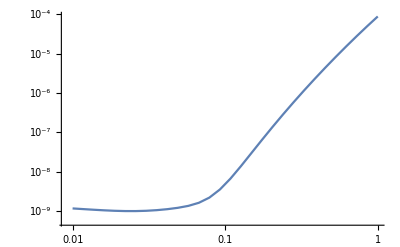

```mathematica
data=Transpose@{times,1-fid};
ListLogLogPlot[data,Joined->True]
```

```mathematica
Re[Log10[1-fid[[1]]]]
```

-8.92476

```mathematica
zero
```

{1,3,6,8,10,11}